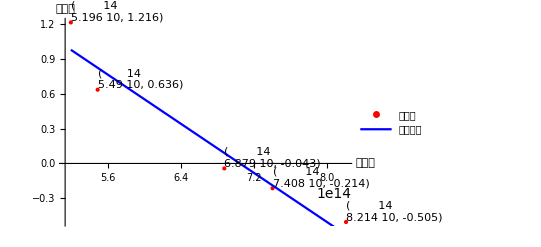

拟合方程: 3.72769-5.28775×10^-15 x

拟合参数： | Estimate | Standard Error | t-Statistic | P-Value
1 | 3.72769 | 0.531052 | 7.01945 | 0.00593893
x | -5.28775×10^-15 | 7.88485×10^-16 | -6.70621 | 0.00676585

决定系数R.b2：0.937465

标准误差：0.0406101

计算得出的斜率: -5.28775×10^-15

h: 8.47097×10^-34

E0: 0.278444

```mathematica
(*定义数据数组*)dataY={-0.505,-0.214,-0.043,0.636,1.216};
dataX={8.214*10^14,7.408*10^14,6.879*10^14,5.490*10^14,5.196*10^14};

(*线性回归拟合*)
fit=LinearModelFit[Transpose[{dataX,dataY}],x,x];

(*获取拟合方程和斜率*)
fitFunction=fit["BestFit"];
slope=fit["BestFitParameters"][[2]];

(*计算 h*)
h=Abs[slope]*(1.602*10^-19);

(*定义 h0*)
h0=6.626*10^-34;

(*计算 E*)
E0=(h-h0)/h0;

(*绘制数据点和拟合直线，并标出数据点的数值和拟合方程*)
Show[ListPlot[Transpose[{dataX,dataY}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"横坐标","纵坐标"},PlotLegends->{"数据点"}],Plot[fitFunction,{x,Min[dataX],Max[dataX]},PlotStyle->Blue,PlotLabel->"一次线性拟合曲线",PlotLegends->{"拟合曲线"}],Epilog->{Text["("<>ToString[dataX[[1]]]<>", "<>ToString[dataY[[1]]]<>")",{dataX[[1]],dataY[[1]]},{-1,-1}],Text["("<>ToString[dataX[[2]]]<>", "<>ToString[dataY[[2]]]<>")",{dataX[[2]],dataY[[2]]},{-1,-1}],Text["("<>ToString[dataX[[3]]]<>", "<>ToString[dataY[[3]]]<>")",{dataX[[3]],dataY[[3]]},{-1,-1}],Text["("<>ToString[dataX[[4]]]<>", "<>ToString[dataY[[4]]]<>")",{dataX[[4]],dataY[[4]]},{-1,-1}],Text["("<>ToString[dataX[[5]]]<>", "<>ToString[dataY[[5]]]<>")",{dataX[[5]],dataY[[5]]},{-1,-1}],Text["拟合直线: y = "<>ToString[Normal[fitFunction],InputForm],{0,8*10^14},{0,1}]}]

(*计算误差分析*)
Print["拟合方程: ",fitFunction];
Print["拟合参数：",fit["ParameterTable"]];
Print["决定系数R.b2：",fit["RSquared"]];
Print["标准误差：",fit["EstimatedVariance"]];
Print["计算得出的斜率: ",slope];
Print["h: ",h];
Print["E0: ",E0];
```

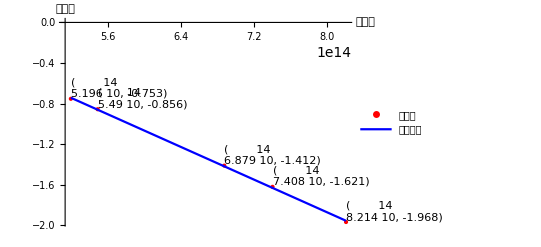

拟合方程: 1.34584-4.0194×10^-15 x

拟合参数： | Estimate | Standard Error | t-Statistic | P-Value
1 | 1.34584 | 0.0321861 | 41.8143 | 0.0000301026
x | -4.0194×10^-15 | 4.77886×10^-17 | -84.1079 | 3.70458×10^-6

决定系数R.b2：0.999576

标准误差：0.000149175

计算得出的斜率: -4.0194×10^-15

h: 6.43908×10^-34

E0: -0.02821

```mathematica
(*定义数据数组*)dataY={-1.968,-1.621,-1.412,-0.856,-0.753};
dataX={8.214*10^14,7.408*10^14,6.879*10^14,5.490*10^14,5.196*10^14};

(*线性回归拟合*)
fit=LinearModelFit[Transpose[{dataX,dataY}],x,x];

(*获取拟合方程和斜率*)
fitFunction=fit["BestFit"];
slope=fit["BestFitParameters"][[2]];

(*计算 h*)
h=Abs[slope]*(1.602*10^-19);

(*定义 h0*)
h0=6.626*10^-34;

(*计算 E*)
E0=(h-h0)/h0;

(*绘制数据点和拟合直线，并标出数据点的数值和拟合方程*)
Show[ListPlot[Transpose[{dataX,dataY}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"横坐标","纵坐标"},PlotLegends->{"数据点"}],Plot[fitFunction,{x,Min[dataX],Max[dataX]},PlotStyle->Blue,PlotLabel->"一次线性拟合曲线",PlotLegends->{"拟合曲线"}],Epilog->{Text["("<>ToString[dataX[[1]]]<>", "<>ToString[dataY[[1]]]<>")",{dataX[[1]],dataY[[1]]},{-1,-1}],Text["("<>ToString[dataX[[2]]]<>", "<>ToString[dataY[[2]]]<>")",{dataX[[2]],dataY[[2]]},{-1,-1}],Text["("<>ToString[dataX[[3]]]<>", "<>ToString[dataY[[3]]]<>")",{dataX[[3]],dataY[[3]]},{-1,-1}],Text["("<>ToString[dataX[[4]]]<>", "<>ToString[dataY[[4]]]<>")",{dataX[[4]],dataY[[4]]},{-1,-1}],Text["("<>ToString[dataX[[5]]]<>", "<>ToString[dataY[[5]]]<>")",{dataX[[5]],dataY[[5]]},{-1,-1}],Text["拟合直线: y = "<>ToString[Normal[fitFunction],InputForm],{0,8*10^14},{0,1}]}]

(*计算误差分析*)
Print["拟合方程: ",fitFunction];
Print["拟合参数：",fit["ParameterTable"]];
Print["决定系数R.b2：",fit["RSquared"]];
Print["标准误差：",fit["EstimatedVariance"]];
Print["计算得出的斜率: ",slope];
Print["h: ",h];
Print["E0: ",E0];
```

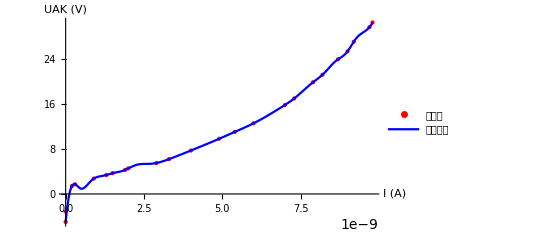

```mathematica
(*定义数据数组*)UAK={-4.97,-3.12,1.40,1.72,2.73,3.35,3.68,4.27,4.53,5.49,6.17,7.7,9.78,11.00,12.52,15.76,16.93,19.8,21.13,23.87,25.27,26.97,29.56,30.40};
I0={0.00*10^-10,0.00*10^-10,2*10^-10,3*10^-10,9*10^-10,13*10^-10,15*10^-10,19*10^-10,20*10^-10,29*10^-10,33*10^-10,40*10^-10,49*10^-10,54*10^-10,60*10^-10,70*10^-10,73*10^-10,79*10^-10,82*10^-10,87*10^-10,90*10^-10,92*10^-10,97*10^-10,98*10^-10};

(*去除一个零值数据点*)
I0NonZero=I0;
UAKNonZero=UAK;
I0NonZero[[2]]=Missing[];
UAKNonZero[[2]]=Missing[];
I0NonZero=DeleteMissing[I0NonZero];
UAKNonZero=DeleteMissing[UAKNonZero];

(*样条拟合*)
splineFit=Interpolation[Transpose[{I0NonZero,UAKNonZero}],Method->"Spline"];

(*绘制数据点和样条拟合曲线，并显示所有数据点*)
plot=Show[ListPlot[Transpose[{I0,UAK}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"I (A)","UAK (V)"},PlotLegends->{"数据点"}],Plot[splineFit[x],{x,Min[I0],Max[I0]},PlotStyle->Blue,PlotLabel->"样条拟合曲线",PlotLegends->{"拟合曲线"}]];

(*显示图像*)
plot
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {2}.

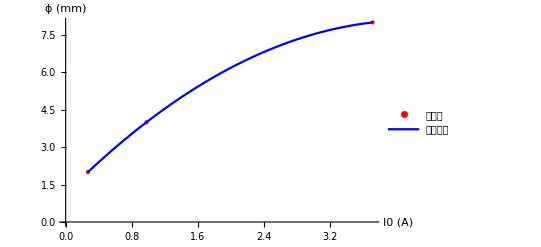

```mathematica
(*定义数据数组*)phi={2,4,8};
I0={27,98,372}*10^10;

(*样条拟合*)
splineFit=Interpolation[Transpose[{I0,phi}],Method->"Spline"];

(*绘制数据点和样条拟合曲线*)
plot=Show[ListPlot[Transpose[{I0,phi}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"

I0 (A)","\[\Phi] (mm)"},PlotLegends->{"数据点"}],Plot[splineFit[x],{x,Min[I0],Max[I0]},PlotStyle->Blue,PlotLabel->"样条拟合曲线",PlotLegends->{"拟合曲线"}]];

(*显示图像*)
plot
```

Interpolation::inhr: 要求的阶数太高；阶数已经被降低为 {2}.

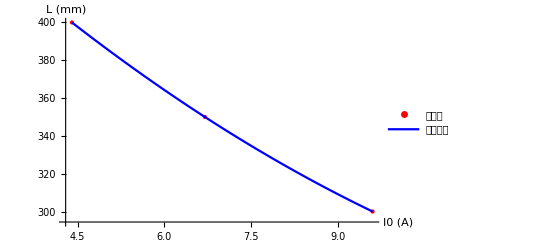

```mathematica
(*定义数据数组*)L={300,350,400};
I0={96,67,44}*10^10;

(*样条拟合*)
splineFit=Interpolation[Transpose[{I0,L}],Method->"Spline"];

(*绘制数据点和样条拟合曲线*)
plot=Show[ListPlot[Transpose[{I0,L}],PlotStyle->{Red,PointSize[Large]},AxesLabel->{"I0 (A)","L (mm)"},PlotLegends->{"数据点"}],Plot[splineFit[x],{x,Min[I0],Max[I0]},PlotStyle->Blue,PlotLabel->"样条拟合曲线",PlotLegends->{"拟合曲线"}]];

(*显示图像*)
plot
```